```mathematica
cc=buildCC2D[{{1,1,1},{1,0,1},{1,1,1}}];
```

```mathematica
a=getNumParent[cc]
```

{{{2,{1,4},{},False},{3,{1,2,5},{},False},{4,{2,3,7,11},{},False},{3,{3,4,13},{},False},{3,{5,6,8},{},False},{4,{6,7,10,16},{},False},{2,{8,9},{},False},{3,{9,10,14},{},False},{4,{11,12,17,20},{},False},{3,{12,13,19},{},False},{3,{14,15,23},{},False},{4,{15,16,20,21},{},False},{3,{17,18,22},{},False},{2,{18,19},{},False},{3,{21,22,24},{},False},{2,{23,24},{},False}},{{1,{1},{1,2},True},{2,{1,2},{2,3},False},{2,{1,4},{3,4},False},{1,{1},{4,1},False},{1,{2},{2,5},True},{2,{2,3},{5,6},False},{1,{2},{6,3},False},{1,{3},{5,7},True},{1,{3},{7,8},False},{2,{3,5},{8,6},False},{1,{4},{3,9},True},{2,{4,6},{9,10},False},{1,{4},{10,4},False},{1,{5},{8,11},True},{2,{5,8},{11,12},False},{1,{5},{12,6},False},{2,{6,7},{9,13},False},{1,{6},{13,14},True},{1,{6},{14,10},False},{1,{7},{9,12},True},{2,{7,8},{12,15},False},{1,{7},{15,13},False},{1,{8},{11,16},True},{1,{8},{16,15},False}},{{0,{},{1,2,3,4},True},{0,{},{5,6,7,2},True},{0,{},{8,9,10,6},True},{0,{},{3,11,12,13},True},{0,{},{10,14,15,16},True},{0,{},{12,17,18,19},True},{0,{},{20,21,22,17},True},{0,{},{15,23,24,21},True}}}

```mathematica
upa=removeKilledParentIndex[a,cc]
```

{{{1,{4},{},False},{1,{2},{},False},{3,{2,3,7},{},False},{3,{3,4,13},{},False},{1,{6},{},False},{4,{6,7,10,16},{},False},{1,{9},{},False},{2,{9,10},{},False},{2,{12,17},{},False},{3,{12,13,19},{},False},{1,{15},{},False},{3,{15,16,21},{},False},{2,{17,22},{},False},{1,{19},{},False},{3,{21,22,24},{},False},{1,{24},{},False}},{{0,{},{},True},{0,{},{2,3},False},{0,{},{3,4},False},{0,{},{4,1},False},{0,{},{},True},{0,{},{5,6},False},{0,{},{6,3},False},{0,{},{},True},{0,{},{7,8},False},{0,{},{8,6},False},{0,{},{},True},{0,{},{9,10},False},{0,{},{10,4},False},{0,{},{},True},{0,{},{11,12},False},{0,{},{12,6},False},{0,{},{9,13},False},{0,{},{},True},{0,{},{14,10},False},{0,{},{},True},{0,{},{12,15},False},{0,{},{15,13},False},{0,{},{},True},{0,{},{16,15},False}},{{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True}}}

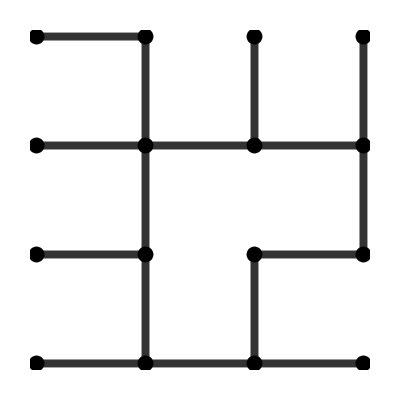

```mathematica
showCC2D[restoreAfterEThinning[upa,cc]]
```

```mathematica
{aa,sp}=updateDisjoint[upa,cc];
aa
sp
```

{{{1,{4},{},True},{1,{2},{},True},{3,{2,3,7},{},False},{3,{3,4,13},{},False},{1,{6},{},True},{4,{6,7,10,16},{},False},{1,{9},{},True},{2,{9,10},{},False},{2,{12,17},{},False},{3,{12,13,19},{},False},{1,{15},{},True},{3,{15,16,21},{},False},{2,{17,22},{},False},{1,{19},{},True},{3,{21,22,24},{},False},{1,{24},{},True}},{{0,{},{},True},{0,{},{2,3},True},{0,{},{3,4},False},{0,{},{4,1},True},{0,{},{},True},{0,{},{5,6},True},{0,{},{6,3},False},{0,{},{},True},{0,{},{7,8},True},{0,{},{8,6},False},{0,{},{},True},{0,{},{9,10},False},{0,{},{10,4},False},{0,{},{},True},{0,{},{11,12},True},{0,{},{12,6},False},{0,{},{9,13},False},{0,{},{},True},{0,{},{14,10},True},{0,{},{},True},{0,{},{12,15},False},{0,{},{15,13},False},{0,{},{},True},{0,{},{16,15},True}},{{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True}}}

7

```mathematica
showCC2D[restoreAfterEThinning[aa,cc]]
```

Part::partw: Part {9,10} of {{3,3},{3,1},{3,5},{3,7},{5,3},{5,1},{5,5},{7,3},{7,5}} does not exist.

Part::partw: Part {10,4} of {{3,3},{3,1},{3,5},{3,7},{5,3},{5,1},{5,5},{7,3},{7,5}} does not exist.

Part::partw: Part {12,6} of {{3,3},{3,1},{3,5},{3,7},{5,3},{5,1},{5,5},{7,3},{7,5}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

```mathematica
upaa=removeKilledParentIndex[aa,cc]
```

{{{0,{},{},True},{0,{},{},True},{2,{3,7},{},False},{2,{3,13},{},False},{0,{},{},True},{3,{7,10,16},{},False},{0,{},{},True},{1,{10},{},False},{2,{12,17},{},False},{2,{12,13},{},False},{0,{},{},True},{2,{16,21},{},False},{2,{17,22},{},False},{0,{},{},True},{2,{21,22},{},False},{0,{},{},True}},{{0,{},{},True},{0,{},{},True},{0,{},{3,4},False},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{6,3},False},{0,{},{},True},{0,{},{},True},{0,{},{8,6},False},{0,{},{},True},{0,{},{9,10},False},{0,{},{10,4},False},{0,{},{},True},{0,{},{},True},{0,{},{12,6},False},{0,{},{9,13},False},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{12,15},False},{0,{},{15,13},False},{0,{},{},True},{0,{},{},True}},{{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True}}}

```mathematica
showCC2D[restoreAfterEThinning[upaa,cc]]
```

Part::partw: Part {9,10} of {{3,3},{3,1},{3,5},{3,7},{5,3},{5,1},{5,5},{7,3},{7,5}} does not exist.

Part::partw: Part {10,4} of {{3,3},{3,1},{3,5},{3,7},{5,3},{5,1},{5,5},{7,3},{7,5}} does not exist.

Part::partw: Part {12,6} of {{3,3},{3,1},{3,5},{3,7},{5,3},{5,1},{5,5},{7,3},{7,5}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

```mathematica
{aaa,sp}=updateDisjoint[upaa,cc];
aaa
sp
```

{{{0,{},{},True},{0,{},{},True},{2,{3,7},{},False},{2,{3,13},{},False},{0,{},{},True},{3,{7,10,16},{},False},{0,{},{},True},{1,{10},{},True},{2,{12,17},{},False},{2,{12,13},{},False},{0,{},{},True},{2,{16,21},{},False},{2,{17,22},{},False},{0,{},{},True},{2,{21,22},{},False},{0,{},{},True}},{{0,{},{},True},{0,{},{},True},{0,{},{3,4},False},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{6,3},False},{0,{},{},True},{0,{},{},True},{0,{},{8,6},True},{0,{},{},True},{0,{},{9,10},False},{0,{},{10,4},False},{0,{},{},True},{0,{},{},True},{0,{},{12,6},False},{0,{},{9,13},False},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{12,15},False},{0,{},{15,13},False},{0,{},{},True},{0,{},{},True}},{{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True}}}

1

```mathematica
upaaa=removeKilledParentIndex[aaa,cc]
```

{{{0,{},{},True},{0,{},{},True},{2,{3,7},{},False},{2,{3,13},{},False},{0,{},{},True},{2,{7,16},{},False},{0,{},{},True},{0,{},{},True},{2,{12,17},{},False},{2,{12,13},{},False},{0,{},{},True},{2,{16,21},{},False},{2,{17,22},{},False},{0,{},{},True},{2,{21,22},{},False},{0,{},{},True}},{{0,{},{},True},{0,{},{},True},{0,{},{3,4},False},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{6,3},False},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{9,10},False},{0,{},{10,4},False},{0,{},{},True},{0,{},{},True},{0,{},{12,6},False},{0,{},{9,13},False},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{12,15},False},{0,{},{15,13},False},{0,{},{},True},{0,{},{},True}},{{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True}}}

```mathematica
{a,b}={3,4}
```

{3,4}

```mathematica
{aaaa,sp}=updateDisjoint[upaaa,cc];
aaaa
sp
```

{{{0,{},{},True},{0,{},{},True},{2,{3,7},{},False},{2,{3,13},{},False},{0,{},{},True},{2,{7,16},{},False},{0,{},{},True},{0,{},{},True},{2,{12,17},{},False},{2,{12,13},{},False},{0,{},{},True},{2,{16,21},{},False},{2,{17,22},{},False},{0,{},{},True},{2,{21,22},{},False},{0,{},{},True}},{{0,{},{},True},{0,{},{},True},{0,{},{3,4},False},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{6,3},False},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{9,10},False},{0,{},{10,4},False},{0,{},{},True},{0,{},{},True},{0,{},{12,6},False},{0,{},{9,13},False},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{12,15},False},{0,{},{15,13},False},{0,{},{},True},{0,{},{},True}},{{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True}}}

0

```mathematica
restoreAfterEThinning[aaaa,cc]
```

{{{3,3},{3,1},{3,5},{5,3},{5,1},{5,5},{7,3},{7,5}},{{3,4},{6,3},{9,10},{10,4},{12,6},{9,13},{12,15},{15,13}},{}}

```mathematica
ncc=restoreAfterEThinning[aaaa,cc]
```

{{{3,3},{3,1},{3,5},{5,3},{5,1},{5,5},{7,3},{7,5}},{{3,4},{6,3},{9,10},{10,4},{12,6},{9,13},{12,15},{15,13}},{}}

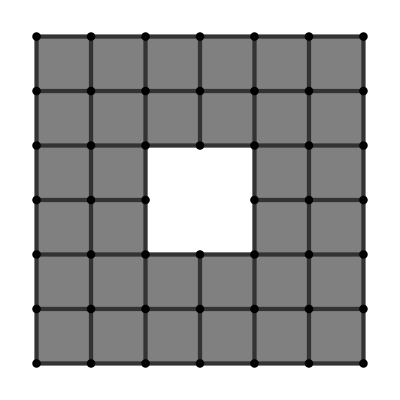

```mathematica
showCC2D[cc2]
```

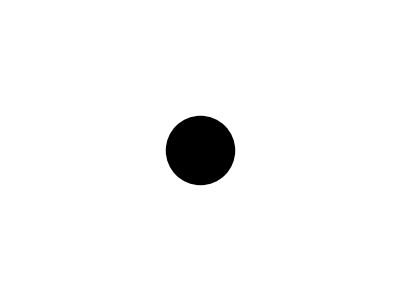

```mathematica
showCC2D[thinExhaustive[buildCC2D[{{1}}]]]
```